```mathematica
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
HEXtoRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

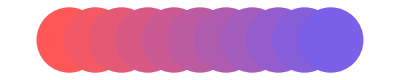

```mathematica
hexColors={"#FF5757","#7A5FE8"};
rgbColors=HEXtoRGB/@hexColors;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
(**)
Graphics[
Table[{
Blend[{
rgbaColors[[1,2]],
rgbaColors[[2,2]]}
,x],Disk[{8x,0}]}
,{x,0,1,1/10}]]
```